# Logistic regression

## Sigmoid function

```mathematica
Sigmoid[z_]:=1/(1+Exp[-z]);
```

```mathematica
{#,N@Sigmoid[#]}&/@Range[-5,5]//TableForm
```

-5 | 0.00669285
-4 | 0.0179862
-3 | 0.0474259
-2 | 0.119203
-1 | 0.268941
0 | 0.5
1 | 0.731059
2 | 0.880797
3 | 0.952574
4 | 0.982014
5 | 0.993307

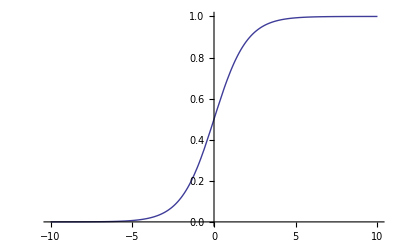

```mathematica
Plot[Sigmoid[x],{x,-10,10}]
```

```mathematica
range=5;
```

```mathematica
$opts={
Mesh->Join[ {Table[{x,Directive[Gray,Dashed]},{x,-range,+range}],Table[{x,Directive[Gray,Dashed]},{x,-range,range}]},{{{0,Directive[Blue]}},{{0,Directive[Red]}}},2],
ColorFunction-> ColorData["DarkRainbow"],
ImageSize-> 600
};
```

```mathematica
Plot3D[Abs[Sigmoid[x+I y]],{x,-range,range},{y,-range,range},AxesLabel->(Style[#,Large]&/@{"Re[z]","Im[z]","Abs[Sigmoid[z]]"}),Evaluate[$opts]]
```

-Graphics3D-

```mathematica
Plot3D[Re[Sigmoid[x+I y]],{x,-range,range},{y,-range,range},AxesLabel->(Style[#,Large]&/@{"Re[z]","Im[z]","Re[Sigmoid[z]]"}), Evaluate[$opts]]
Plot3D[Im[Sigmoid[x+I y]],{x,-range,range},{y,-range,range},AxesLabel->(Style[#,Large]&/@{"Re[z]","Im[z]","Im[Sigmoid[z]]"}),Evaluate[$opts]]
```

-Graphics3D-

-Graphics3D-

## Binary linear logistic regression

### Example data

There are two data files in CSV format.

```mathematica
$dataFile1=ToFileName[{NotebookDirectory[]},"ex2data1.txt"];
$dataFile2=ToFileName[{NotebookDirectory[]},"ex2data2.txt"];
```

The data files happen to be CSV file, import as so.

```mathematica
data1=Import[$dataFile1,"CSV"];
data2=Import[$dataFile2,"CSV"];
```

```mathematica
ex1=data1[[All,{1,2}]];
```

```mathematica
X1=Prepend[#,1]&/@ex1;
y1=data1[[All,3]];
```

```mathematica
X1//RandomChoice
```

{1,74.7893,41.5734}

Visualize the feature matrix X:

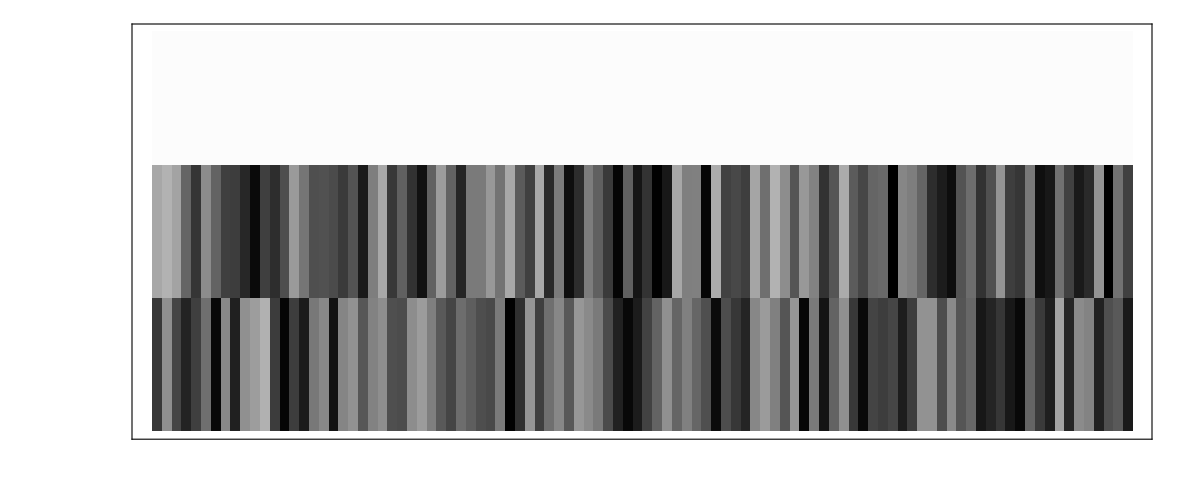

```mathematica
X1//Transpose//ArrayPlot[#,ImageSize-> 1200,Frame-> True,PlotRangePadding-> None]&
```

Find the data points in the “admitted” and “not admitted” types:

```mathematica
ex1Admitted=Cases[data1,{x_,y_,1}:> {x,y}];
ex1NotAdmitted=Cases[data1,{x_,y_,0}:> {x,y}];
```

Plot it in the parameter space to get an idea of distribution:

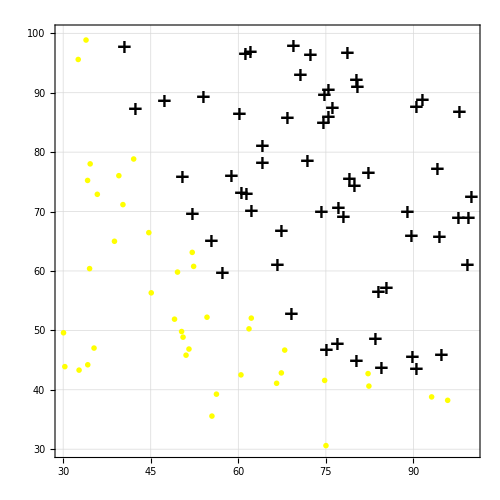

```mathematica
plotTrainingData1=ListPlot[{ex1Admitted,ex1NotAdmitted},
ImageSize-> 500,AspectRatio-> 1,
Frame-> True,GridLines-> Automatic,PlotRange-> {{30,100},{30,100}},
PlotStyle-> {Directive[Black,PointSize[Large]],Directive[Yellow,PointSize[Large]]},
PlotMarkers-> {Style["+",FontSize-> 20,FontWeight-> Bold],Graphics[{EdgeForm[Thick],Yellow,Disk[{0,0},Scaled[0.02]]}]}
]
```

```mathematica
ex2=data2[[All,{1,2}]];
```

```mathematica
X2=Prepend[#,1]&/@ex2;
y2=data2[[All,3]];
```

```mathematica
X2//RandomChoice
```

{1,0.29896,0.61915}

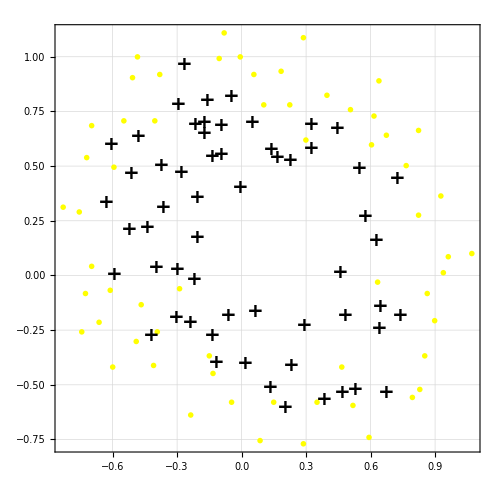

```mathematica
ex2Admitted=Cases[data2,{x_,y_,1}:> {x,y}];
ex2NotAdmitted=Cases[data2,{x_,y_,0}:> {x,y}];
plotTrainingData2=ListPlot[{ex2Admitted,ex2NotAdmitted},
ImageSize-> 500,AspectRatio-> Automatic,
Frame-> True,GridLines-> Automatic,PlotRange-> Automatic,
PlotStyle-> {Directive[Black,PointSize[Large]],Directive[Yellow,PointSize[Large]]},
PlotMarkers-> {Style["+",FontSize-> 20,FontWeight-> Bold],Graphics[{EdgeForm[Thick],Yellow,Disk[{0,0},Scaled[0.02]]}]}
]
```

### Cost function

Hypothesis function h as a function of fitting parameter and feature matrix:

```mathematica
h[β_,X_]:=Sigmoid[X.β];
```

Cost function J as a function of fitting parameter and the example data set including the feature matrix X and the observed dependent variable y:

```mathematica
J[β_,X_,y_]:=-1/Length[y](y.Log[h[β,X]]+(1-y).Log[1-h[β,X]])
```

Define the fitting parameter in to the vector with right dimension:

```mathematica
Clear[β]
β=Table[Symbol["β"<>ToString[j]],{j,0,Length[X1[[1]]]-1}]
```

{β0,β1,β2}

Cost function at {0, 0, 0}

```mathematica
J[{0,0,0},X1,y1]
```

0.693147

### Find β to minimize cost function

#### Use NMinimize

Using NMinimize naively causes NMinimize::nnum error as the function J has singularity at {β0, β1, β2} = {0.673558, 0.659492, 0.0861047}

```mathematica
NMinimize[J[{β0,β1,β2},X1,y1],{β0,β1,β2}];
```

NMinimize::nnum: The function value Indeterminate is not a number at {β0, β1, β2} = {0.673558, 0.659492, 0.0861047}.

```mathematica
regularize[Indeterminate]:=$MaxMachineNumber;
regularize[x_?NumericQ]:=x
```

```mathematica
res=NMinimize[regularize@J[{β0,β1,β2},X1,y1],{β0,β1,β2}];//AbsoluteTiming
```

{0.970877,Null}

```mathematica
res
```

{0.203498,{β0→-25.1613,β1→0.206232,β2→0.201472}}

#### Use FindMinimum

Using NMinimize naively causes NMinimize::nnum error as the function J has singularity at {β0, β1, β2} = {0.673558, 0.659492, 0.0861047}

```mathematica
FindMinimum[J[{β0,β1,β2},X1,y1],{β0,0},{β1,0},{β2,0}]
```

FindMinimum::nrnum: The function value Indeterminate is not a real number at {β0, β1, β2} = {0.00303682, 0.364698, 0.342032}.

{0.693147,{β0→0.,β1→0.,β2→0.}}

```mathematica
regularize[Indeterminate]:=$MaxMachineNumber;
regularize[x_?NumericQ]:=x
```

```mathematica
res=FindMinimum[regularize@J[{β0,β1,β2},X1,y1],{β0,0},{β1,0},{β2,0}];//AbsoluteTiming
```

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

{0.055851,Null}

```mathematica
res
```

{0.693147,{β0→0.,β1→0.,β2→0.}}

```mathematica
res
```

{0.693147,{β0→0.,β1→0.,β2→0.}}

#### Use LogitModelFit

```mathematica
data=Join[X1,List/@y1,2];
```

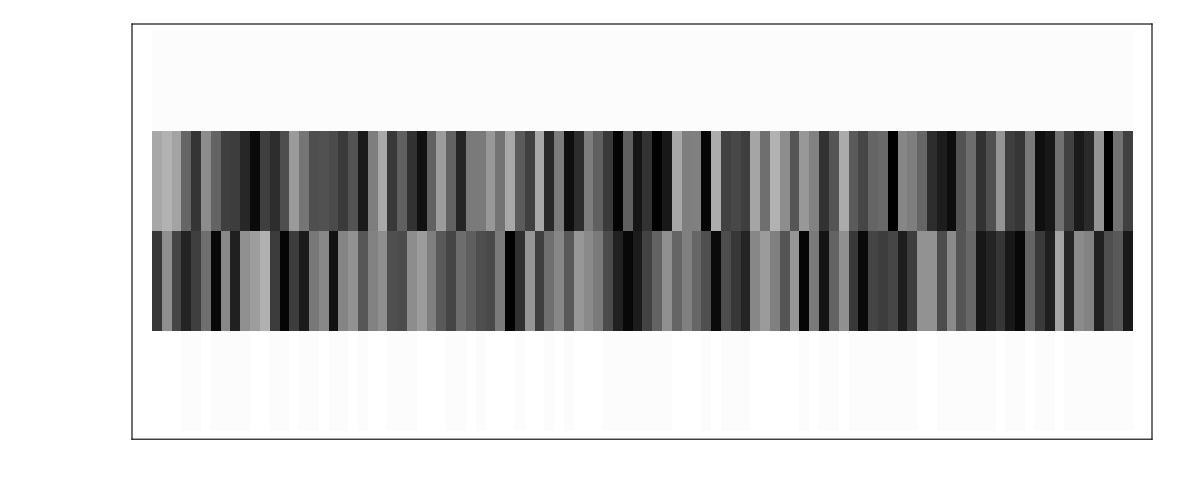

```mathematica
data//Transpose//ArrayPlot[#,ImageSize-> 1200,Frame-> True,PlotRangePadding-> None]&
```

```mathematica
logit1=LogitModelFit[data,{β0,β1,β2},{β0,β1,β2},IncludeConstantBasis-> False]
```

FittedModel[1/(1+ⅇ^(25.1613 β0-«1»-«20» β2))]

```mathematica
Normal[logit1]
```

1/(1+ⅇ^(25.1613 β0-0.206232 β1-0.201472 β2))

```mathematica
βFit=logit1["BestFitParameters"]
```

{-25.1613,0.206232,0.201472}

Include constant basis:

```mathematica
data=Join[ex1,List/@y1,2];
```

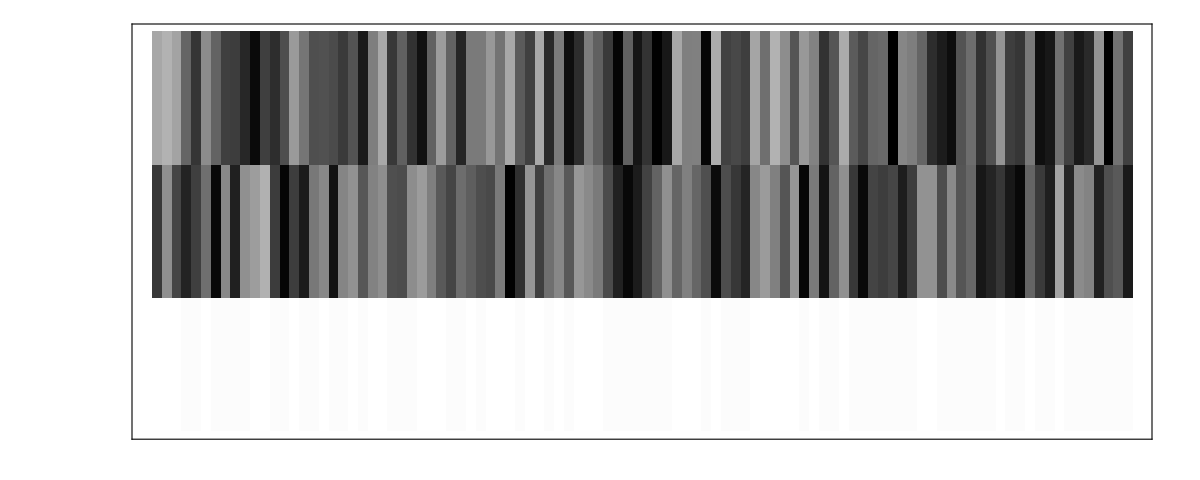

```mathematica
data//Transpose//ArrayPlot[#,ImageSize-> 1200,Frame-> True,PlotRangePadding-> None]&
```

```mathematica
logit2=LogitModelFit[data,{β1,β2},{β1,β2},IncludeConstantBasis-> True]
```

FittedModel[1/(1+ⅇ^(25.1613-«1»-«20» β2))]

```mathematica
Normal[logit2]
```

1/(1+ⅇ^(25.1613-0.206232 β1-0.201472 β2))

```mathematica
logit2["BestFitParameters"]
```

{-25.1613,0.206232,0.201472}

```mathematica
logit2["DevianceResiduals"]
```

{-0.436915,-0.00919343,-0.299673,0.138719,0.0600478,-0.147352,0.045219,1.31137,0.0240841,0.784037,-2.19287,-0.240888,0.0382131,0.0170918,-0.582489,0.196083,1.3033,-0.567618,0.024228,1.05322,-0.371949,0.0524155,-0.12203,-0.0142239,0.12771,0.559637,1.01028,-2.00192,-0.440317,-0.184239,0.465948,0.195677,-0.580195,1.36869,-0.39248,-0.259504,-1.95569,0.1582,-0.675486,-0.318908,0.245559,-0.110788,0.0328225,-1.18129,-0.0948556,-0.542896,0.118599,0.00276377,0.0398848,0.00429865,0.0615631,0.0316112,0.446772,-0.0749678,-0.130837,-0.329669,0.016934,-1.53832,0.170936,0.0925259,0.0306092,-0.0210903,-0.083804,-0.015942,-0.385626,-0.288912,0.338165,-0.142278,0.00975229,0.828825,-0.0111392,0.213837,0.0146046,0.495955,0.446216,0.00949699,0.414464,0.966662,-0.1787,-1.35275,0.0378883,0.23189,0.472132,1.78527,0.0108585,0.063554,-0.935759,0.018973,0.00731973,-0.475653,0.0105876,0.005436,-0.0533909,0.0368371,0.396046,0.552099,0.756977,0.0143805,1.47034,0.0223203}

Alternatively, use the GeneralizedLinearModelFit with ExponentialFamily → “Binomial”, LinkFunction→Automatic:

```mathematica
GeneralizedLinearModelFit [data,{β1,β2},{β1,β2},IncludeConstantBasis-> True,ExponentialFamily -> "Binomial", LinkFunction->Automatic]
```

FittedModel[1/(1+ⅇ^(25.1613-«1»-«20» β2))]

Examine deviance residuals:

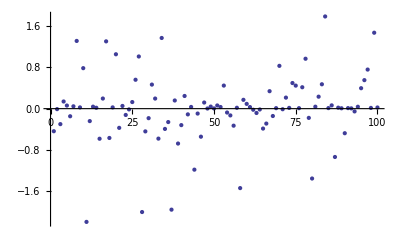

```mathematica
ListPlot[logit2["DevianceResiduals"]]
```

Cost function’s value at fitted parameters:

```mathematica
fittedParam=MapThread[Rule,{{β0,β1,β2},logit2["BestFitParameters"]}]
```

{β0→-25.1613,β1→0.206232,β2→0.201472}

```mathematica
J[{β0,β1,β2},X1,y1]/.fittedParam
```

0.203498

### Decision boundary

```mathematica
Total[βFit*{1,x1,x2}]==0
```

-25.1613+0.206232 x1+0.201472 x2==0

```mathematica
sol=Solve[Total[βFit*{1,x1,x2}]==0,x2]
```

{{x2→4.96348 (25.1613-0.206232 x1)}}

```mathematica
sol[[1,1,2]]
```

4.96348 (25.1613-0.206232 x1)

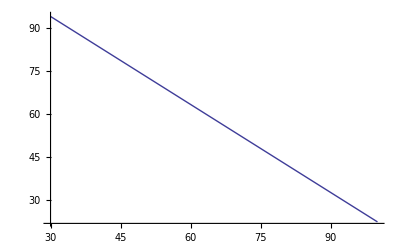

```mathematica
plotDecisionBoundary=Plot[sol[[1,1,2]],{x1,30,100}]
```

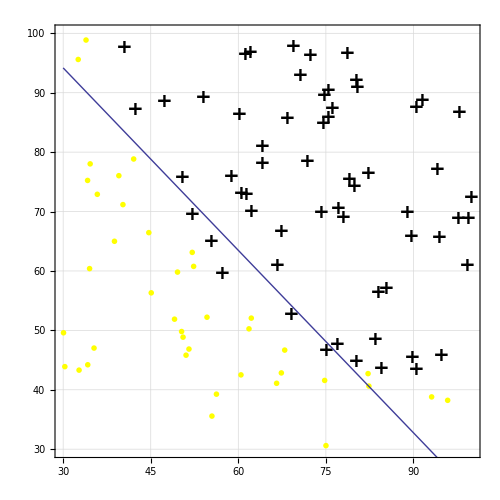

```mathematica
Show[{plotTrainingData1,plotDecisionBoundary}]
```

### Prediction

```mathematica
Normal[logit2]
```

1/(1+ⅇ^(25.1613-0.206232 β1-0.201472 β2))

```mathematica
predictedProb[x1_,x2_]:=Block[
{β1,β2,sol},
sol=MapThread[Rule,{{β1,β2},{x1,x2}}];
Normal[logit2]/.sol
]
```

```mathematica
predictedProb[45,85]
```

0.776291

### Prediction accuracy

```mathematica
predict[x1_,x2_]:=If[predictedProb[x1,x2]≥ 0.5,1,0]
```

```mathematica
Count[Map[predict@@#&,ex1]-y1,0]/Length[y1]//N
```

0.89

## Binary non-linear logistic regression

### Example data

There are two data files in CSV format.

```mathematica
$dataFile=ToFileName[{NotebookDirectory[]},"ex2data2.txt"];
```

The data files happen to be CSV file, import as so.

```mathematica
data=Import[$dataFile,"CSV"];
```

```mathematica
featureData=data[[All,{1,2}]];
```

```mathematica
X=Prepend[#,1]&/@featureData;
y=data[[All,3]];
```

```mathematica
X//RandomChoice
```

{1,0.93836,0.012427}

```mathematica
y//Length
```

118

Visualize the feature matrix X:

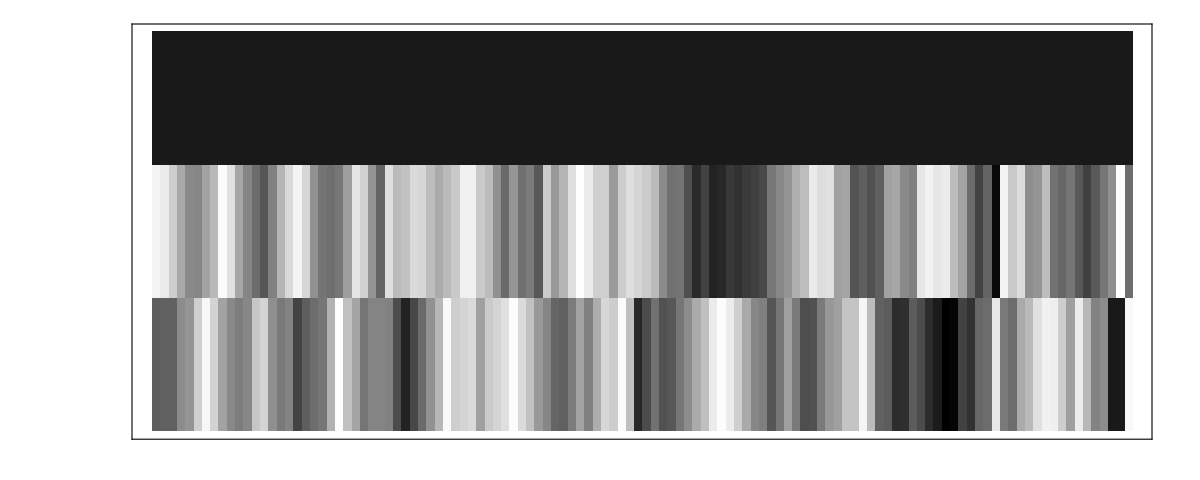

```mathematica
X//Transpose//ArrayPlot[#,ImageSize-> 1200,Frame-> True,PlotRangePadding-> None]&
```

Find the data points in the “admitted” and “not admitted” types:

```mathematica
exAdmitted=Cases[data,{x_,y_,1}:> {x,y}];
exNotAdmitted=Cases[data,{x_,y_,0}:> {x,y}];
```

```mathematica
exAdmitted//{Max[#],Min[#]}&
```

{0.96272,-0.62846}

Plot it in the parameter space to get an idea of distribution:

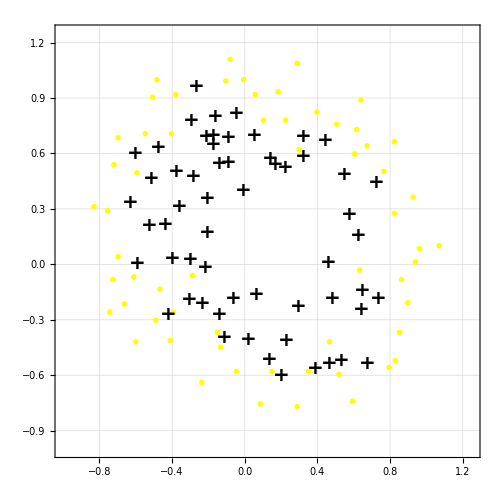

```mathematica
plotTrainingData=ListPlot[{exAdmitted,exNotAdmitted},
ImageSize-> 500,AspectRatio-> 1,
Frame-> True,GridLines-> Automatic,PlotRange-> {{-1,1.25},{-1,1.25}},
PlotStyle-> {Directive[Black,PointSize[Large]],Directive[Yellow,PointSize[Large]]},
PlotMarkers-> {Style["+",FontSize-> 20,FontWeight-> Bold],Graphics[{EdgeForm[Thick],Yellow,Disk[{0,0},Scaled[0.02]]}]}
]
```

### Feature mapping: generating non-linear features from original features x1, x2

```mathematica
X
```

{{1,0.051267,0.69956},{1,-0.092742,0.68494},{1,-0.21371,0.69225},{1,-0.375,0.50219},{1,-0.51325,0.46564},{1,-0.52477,0.2098},{1,-0.39804,0.034357},{1,-0.30588,-0.19225},{1,0.016705,-0.40424},{1,0.13191,-0.51389},{1,0.38537,-0.56506},{1,0.52938,-0.5212},{1,0.63882,-0.24342},{1,0.73675,-0.18494},{1,0.54666,0.48757},{1,0.322,0.5826},{1,0.16647,0.53874},{1,-0.046659,0.81652},{1,-0.17339,0.69956},{1,-0.47869,0.63377},{1,-0.60541,0.59722},{1,-0.62846,0.33406},{1,-0.59389,0.005117},{1,-0.42108,-0.27266},{1,-0.11578,-0.39693},{1,0.20104,-0.60161},{1,0.46601,-0.53582},{1,0.67339,-0.53582},{1,-0.13882,0.54605},{1,-0.29435,0.77997},{1,-0.26555,0.96272},{1,-0.16187,0.8019},{1,-0.17339,0.64839},{1,-0.28283,0.47295},{1,-0.36348,0.31213},{1,-0.30012,0.027047},{1,-0.23675,-0.21418},{1,-0.06394,-0.18494},{1,0.062788,-0.16301},{1,0.22984,-0.41155},{1,0.2932,-0.2288},{1,0.48329,-0.18494},{1,0.64459,-0.14108},{1,0.46025,0.012427},{1,0.6273,0.15863},{1,0.57546,0.26827},{1,0.72523,0.44371},{1,0.22408,0.52412},{1,0.44297,0.67032},{1,0.322,0.69225},{1,0.13767,0.57529},{1,-0.0063364,0.39985},{1,-0.092742,0.55336},{1,-0.20795,0.35599},{1,-0.20795,0.17325},{1,-0.43836,0.21711},{1,-0.21947,-0.016813},{1,-0.13882,-0.27266},{1,0.18376,0.93348},{1,0.22408,0.77997},{1,0.29896,0.61915},{1,0.50634,0.75804},{1,0.61578,0.7288},{1,0.60426,0.59722},{1,0.76555,0.50219},{1,0.92684,0.3633},{1,0.82316,0.27558},{1,0.96141,0.085526},{1,0.93836,0.012427},{1,0.86348,-0.082602},{1,0.89804,-0.20687},{1,0.85196,-0.36769},{1,0.82892,-0.5212},{1,0.79435,-0.55775},{1,0.59274,-0.7405},{1,0.51786,-0.5943},{1,0.46601,-0.41886},{1,0.35081,-0.57968},{1,0.28744,-0.76974},{1,0.085829,-0.75512},{1,0.14919,-0.57968},{1,-0.13306,-0.4481},{1,-0.40956,-0.41155},{1,-0.39228,-0.25804},{1,-0.74366,-0.25804},{1,-0.69758,0.041667},{1,-0.75518,0.2902},{1,-0.69758,0.68494},{1,-0.4038,0.70687},{1,-0.38076,0.91886},{1,-0.50749,0.90424},{1,-0.54781,0.70687},{1,0.10311,0.77997},{1,0.057028,0.91886},{1,-0.10426,0.99196},{1,-0.081221,1.1089},{1,0.28744,1.087},{1,0.39689,0.82383},{1,0.63882,0.88962},{1,0.82316,0.66301},{1,0.67339,0.64108},{1,1.0709,0.10015},{1,-0.046659,-0.57968},{1,-0.23675,-0.63816},{1,-0.15035,-0.36769},{1,-0.49021,-0.3019},{1,-0.46717,-0.13377},{1,-0.28859,-0.060673},{1,-0.61118,-0.067982},{1,-0.66302,-0.21418},{1,-0.59965,-0.41886},{1,-0.72638,-0.082602},{1,-0.83007,0.31213},{1,-0.72062,0.53874},{1,-0.59389,0.49488},{1,-0.48445,0.99927},{1,-0.0063364,0.99927},{1,0.63265,-0.030612}}

```mathematica
sortfun[expr_]:={Log[10,expr/.{x1-> 10,x2-> 10}],Log[10,expr/.{x1-> 1,x2-> 10}],Log[10,expr/.{x1-> 10,x2-> 1}]};
```

```mathematica
nonLinearFeatures=SortBy[Flatten[Table[Table[x1^p1 x2^p2,{p1,0,6-p2}],{p2,0,6}]],sortfun]
```

{1,x1,x2,x1^2,x1 x2,x2^2,x1^3,x1^2 x2,x1 x2^2,x2^3,x1^4,x1^3 x2,x1^2 x2^2,x1 x2^3,x2^4,x1^5,x1^4 x2,x1^3 x2^2,x1^2 x2^3,x1 x2^4,x2^5,x1^6,x1^5 x2,x1^4 x2^2,x1^3 x2^3,x1^2 x2^4,x1 x2^5,x2^6}

```mathematica
XNonlinear=Map[nonLinearFeatures/.#&,MapThread[Rule,{{x0,x1,x2},#}]&/@X];
```

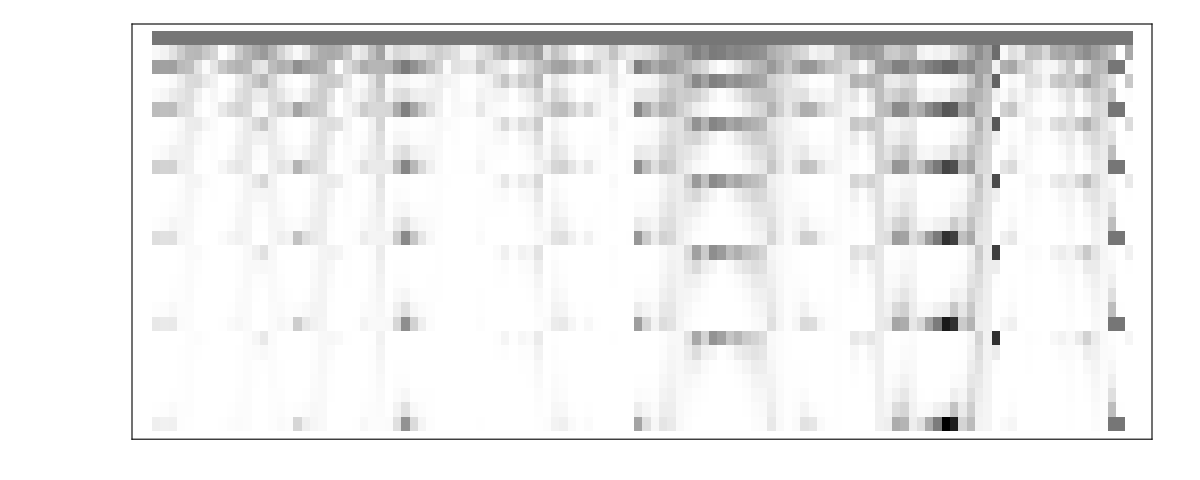

```mathematica
XNonlinear//Transpose//ArrayPlot[#,ImageSize-> 1200,Frame-> True,PlotRangePadding-> None]&
```

### Cost function

Hypothesis function h as a function of fitting parameter and feature matrix:

```mathematica
h[β_,X_]:=Sigmoid[X.β];
```

Cost function J as a function of fitting parameter and the example data set including the feature matrix X and the observed dependent variable y:

```mathematica
J[β_,X_,y_]:=-1/Length[y](y.Log[h[β,X]]+(1-y).Log[1-h[β,X]])
```

Cost function J with regularization:

```mathematica
J[β_,X_,y_,λ_]:=-1/Length[y](y.Log[h[β,X]]+(1-y).Log[1-h[β,X]])+λ/(2*Length[y])β.β
```

Define the fitting parameter in to the vector with right dimension:

```mathematica
Clear[β]
β=Table[Symbol["β"<>ToString[j]],{j,0,Length[XNonlinear[[1]]]-1}]
```

{β0,β1,β2,β3,β4,β5,β6,β7,β8,β9,β10,β11,β12,β13,β14,β15,β16,β17,β18,β19,β20,β21,β22,β23,β24,β25,β26,β27}

Cost function at βInit = {0, 0, 0, ..., 0}

```mathematica
βInit=Table[0,{Length[XNonlinear[[1]]]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
J[βInit,XNonlinear,y]
```

0.693147

```mathematica
λInit=1;
```

```mathematica
J[βInit,XNonlinear,y,λInit]
```

0.693147

### Find β to minimize cost function

#### Use NMinimize

Using NMinimize naively causes NMinimize::nnum error as the function J has singularity at {β0,β1,β10,β11,β12,β13,β14,β15,β16,β17,β18,β19,β2,β20,β21,β22,β23,β24,β25,β26,β27,β3,β4,β5,β6,β7,β8,β9,λ} = {12.6559,18.8815,-29.085,-51.1986,29.671,16.936,-80.5918,-33.3686,-37.909,-32.1894,12.2811,50.7038,-23.9778,-28.0593,«18»,-18.4441,43.3584,59.3545,-63.1989,39.4808,-6.06265,-69.0835,-23.0398,35.274,-3.6493,24.3274,-77.6666,-24.3271,-72.0648}

```mathematica
J[β,XNonlinear,y]
```

```mathematica
res=TimeConstrained[NMinimize[J[β,XNonlinear,y,λ],param,MaxIterations-> 1000],300];//AbsoluteTiming
```

NMinimize::nnum: The function value Indeterminate is not a number at {β0, β1, β10, β11, β12, β13, β14, β15, β16, β17, β18, β19, β2, β20, β21, β22, β23, β24, β25, β26, β27, β3, β4, β5, β6, β7, β8, β9, λ} = {20.5131, -36.2166, -138.016, -90.5155, -48.4352, 4.62162, -43.1958, 14.7424, -60.77, -28.0367, 10.171, -61.049, 22.9667, -86.1667, 62.2575, 61.3729, 8.59384, 94.443, -62.4157, -8.53869, -46.2864, -64.3282, -21.4385, 15.8534, -51.9543, -64.9123, -95.8589, -44.8861, -143.193}.

{1.62123,Null}

Regularize J removing its singularities:

```mathematica
regularize[Indeterminate]:=$MaxMachineNumber;
regularize[x_?NumericQ]:=x
```

```mathematica
res=NMinimize[regularize@J[β,XNonlinear,y,1],Evaluate[β]];//AbsoluteTiming
```

{12.97371,Null}

```mathematica
res
```

{0.53516,{β0→1.14213,β1→0.601321,β2→1.16718,β3→-1.87175,β4→-0.915734,β5→-1.26953,β6→0.126683,β7→-0.368731,β8→-0.345184,β9→-0.173776,β10→-1.42386,β11→-0.0485564,β12→-0.60642,β13→-0.269318,β14→-1.16316,β15→-0.243101,β16→-0.207074,β17→-0.0431849,β18→-0.280281,β19→-0.286956,β20→-0.469105,β21→-1.03618,β22→0.0292351,β23→-0.292622,β24→0.0173668,β25→-0.328972,β26→-0.13796,β27→-0.93199}}

```mathematica
JMinNMinimize=res[[1]]
βFitNMinimize=res[[2]]
```

0.53516

{β0→1.14213,β1→0.601321,β2→1.16718,β3→-1.87175,β4→-0.915734,β5→-1.26953,β6→0.126683,β7→-0.368731,β8→-0.345184,β9→-0.173776,β10→-1.42386,β11→-0.0485564,β12→-0.60642,β13→-0.269318,β14→-1.16316,β15→-0.243101,β16→-0.207074,β17→-0.0431849,β18→-0.280281,β19→-0.286956,β20→-0.469105,β21→-1.03618,β22→0.0292351,β23→-0.292622,β24→0.0173668,β25→-0.328972,β26→-0.13796,β27→-0.93199}

#### Use FindMinimum

Using NMinimize naively causes NMinimize::nnum error as the function J has singularity at {β0, β1, β2} = {0.673558, 0.659492, 0.0861047}

```mathematica
FindMinimum[J[{β0,β1,β2},X1,y1],{β0,0},{β1,0},{β2,0}]
```

Power::infy: Infinite expression 1/0 encountered.

FindMinimum::nrnum: The function value ComplexInfinity is not a real number at {β0, β1, β2} = {0., 0., 0.}.

FindMinimum[J[{β0,β1,β2},X1,y1],{β0,0},{β1,0},{β2,0}]

```mathematica
regularize[Indeterminate]:=$MaxMachineNumber;
regularize[x_?NumericQ]:=x
```

```mathematica
res=FindMinimum[regularize@J[{β0,β1,β2},X1,y1],{β0,0},{β1,0},{β2,0}];//AbsoluteTiming
```

Power::infy: Infinite expression 1/0 encountered.

FindMinimum::nrnum: The function value regularize[ComplexInfinity] is not a real number at {β0, β1, β2} = {0., 0., 0.}.

Power::infy: Infinite expression 1/0 encountered.

FindMinimum::nrnum: The function value regularize[ComplexInfinity] is not a real number at {β0, β1, β2} = {0., 0., 0.}.

{0.00238,Null}

```mathematica
res
```

Power::infy: Infinite expression 1/0 encountered.

FindMinimum::nrnum: The function value regularize[ComplexInfinity] is not a real number at {β0, β1, β2} = {0., 0., 0.}.

FindMinimum[regularize[J[{β0,β1,β2},X1,y1]],{β0,0},{β1,0},{β2,0}]

```mathematica
res
```

Power::infy: Infinite expression 1/0 encountered.

FindMinimum::nrnum: The function value regularize[ComplexInfinity] is not a real number at {β0, β1, β2} = {0., 0., 0.}.

FindMinimum[regularize[J[{β0,β1,β2},X1,y1]],{β0,0},{β1,0},{β2,0}]

#### Use LogitModelFit without constant basis

```mathematica
data=Join[XNonlinear,List/@y,2];
```

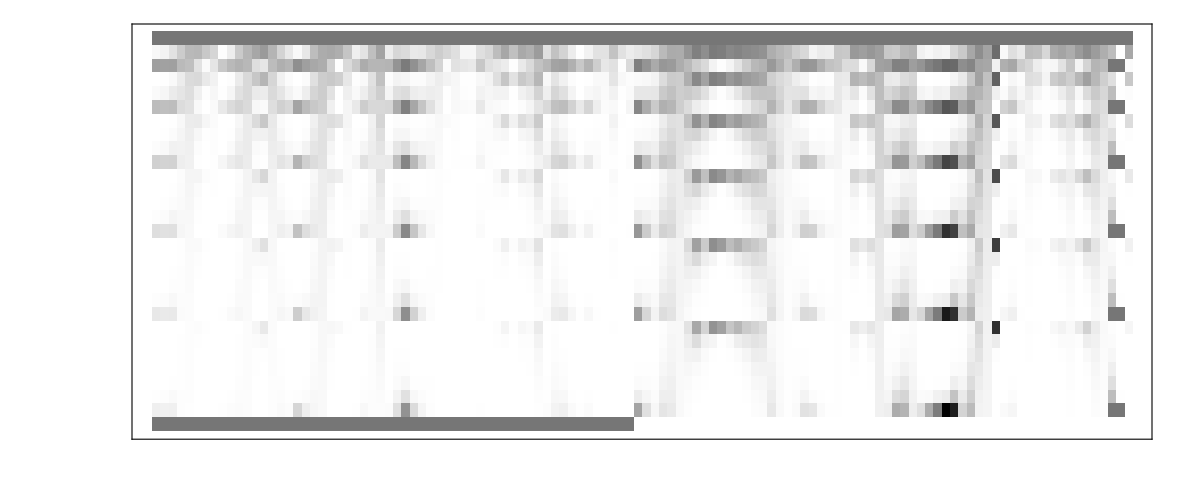

```mathematica
data//Transpose//ArrayPlot[#,ImageSize-> 1200,Frame-> True,PlotRangePadding-> None]&
```

```mathematica
logitModelFit1=LogitModelFit[data,Evaluate[β],Evaluate[β],IncludeConstantBasis-> False];//AbsoluteTiming
logitModelFit1
```

{0.18081,Null}

FittedModel[1/(1+ⅇ^(«1»))]

```mathematica
Normal[logit1]
```

logit1

```mathematica
βFitLogitModel1=MapThread[Rule,{Evaluate[β],logit1["BestFitParameters"]}]
```

MapThread::mptd: Object logit1["BestFitParameters"] at position {2, 2} in MapThread[Rule, {{β0, β1, β2, β3, β4, β5, β6, β7, β8, β9, β10, β11, β12, β13, β14, β15, β16, β17, β18, β19, β20, β21, β22, β23, β24, β25, β26, β27}, logit1["BestFitParameters"]}] has only 0 of required 1 dimensions.

MapThread[Rule,{{β0,β1,β2,β3,β4,β5,β6,β7,β8,β9,β10,β11,β12,β13,β14,β15,β16,β17,β18,β19,β20,β21,β22,β23,β24,β25,β26,β27},logit1[BestFitParameters]}]

#### Use LogitModelFit including constant basis

Include constant basis:

```mathematica
data=Join[XNonlinear[[All,2;;]],List/@y,2];
```

```mathematica
data[[1]]//Length
```

28

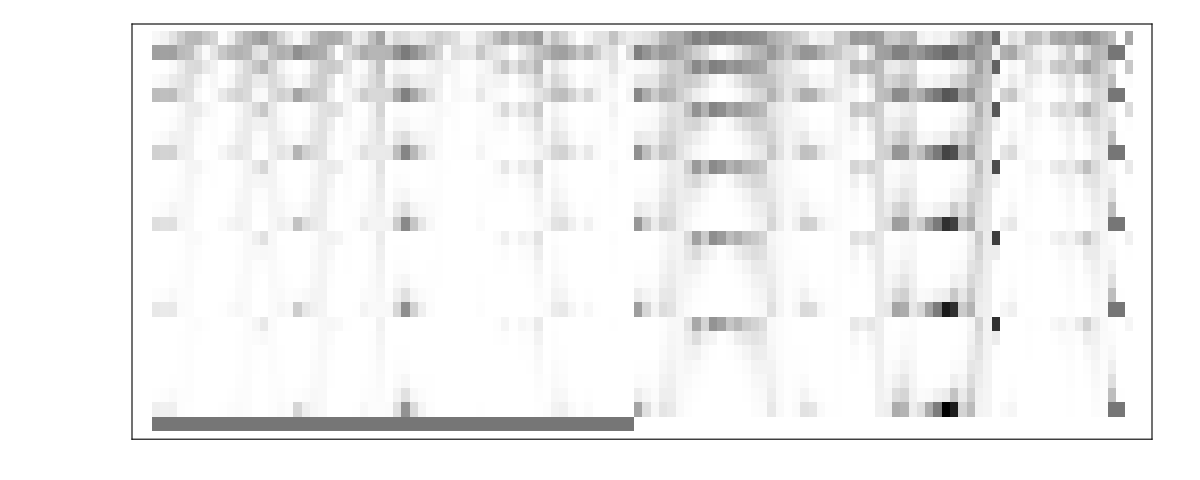

```mathematica
data//Transpose//ArrayPlot[#,ImageSize-> 1200,Frame-> True,PlotRangePadding-> None]&
```

```mathematica
logitModel2=LogitModelFit[data,Evaluate[β[[2;;]]],Evaluate[β[[2;;]]],IncludeConstantBasis-> True]
```

FittedModel[1/(1+ⅇ^(«40»+«19» β9))]

```mathematica
Normal[logitModel2]
```

1/(1+ⅇ^(-38.2308-55.5958 β1-1182.7 β10-1279.34 β11-1907.9 β12-914.319 β13-514.28 β14-573.223 β15-1629.75 β16-2553.6 β17-2919.07 β18-1780.61 β19-98.1467 β2-785.315 β20+1257.91 β21+2260.01 β22+4142.8 β23+4290.59 β24+4229.65 β25+2055.55 β26+750.381 β27+369.43 β3+177.12 β4+194.261 β5+366.009 β6+842.211 β7+719.448 β8+511.895 β9))

```mathematica
βFitLogitModel1=MapThread[Rule,{Evaluate[β],logitModel2["BestFitParameters"]}]
```

{β0→38.2308,β1→55.5958,β2→98.1467,β3→-369.43,β4→-177.12,β5→-194.261,β6→-366.009,β7→-842.211,β8→-719.448,β9→-511.895,β10→1182.7,β11→1279.34,β12→1907.9,β13→914.319,β14→514.28,β15→573.223,β16→1629.75,β17→2553.6,β18→2919.07,β19→1780.61,β20→785.315,β21→-1257.91,β22→-2260.01,β23→-4142.8,β24→-4290.59,β25→-4229.65,β26→-2055.55,β27→-750.381}

```mathematica
logitModel2["DevianceResiduals"]
```

{0.501405,0.0754926,0.101672,0.0172188,0.284729,0.790648,1.02276,1.50753,0.324581,0.483542,1.07941,0.673625,0.394382,0.112535,0.00113704,0.74072,0.126651,0.4061,0.0962092,1.03483,1.23647,0.459204,0.724525,1.58091,0.995986,1.34934,0.971655,0.311366,0.000237684,0.659039,0.447376,0.269887,0.0228124,0.000301804,0.00235873,0.0403249,1.06497,0.00254088,0.0000174109,0.226495,0.00411086,0.626823,0.78937,0.36245,0.294399,0.138725,0.464401,0.399455,0.544221,1.07768,0.17406,1.51963×10^-7,0.000355657,4.99578×10^-7,6.485×10^-7,0.201719,0.00218419,0.448789,0.,-0.149538,-1.51288,0.,0.,-0.678739,0.,0.,-0.00169642,0.,0.,-0.0067379,-0.0000715603,-0.241466,-0.00524563,-0.0119092,-3.13279×10^-7,-0.834553,-1.42578,-1.25913,-6.14391×10^-8,0.,-1.23653,-0.678664,-2.28644×10^-6,-1.24593,0.,-0.00607516,-0.00716879,-0.00919889,-1.14566,-0.511588,-0.00583675,-0.280337,-0.897576,-0.0152878,-0.186446,0.,0.,0.,0.,0.,0.,0.,-0.00873107,0.,-1.271,-0.00181789,-1.70045,-2.4856,-0.445784,0.,0.,0.,0.,-0.185003,-2.10811,-0.000188003,-0.000102235,-1.0534}

#### Using GeneralizedLinearModelFit

Alternatively, use the GeneralizedLinearModelFit with ExponentialFamily → “Binomial”, LinkFunction→Automatic:

```mathematica
generalizedLinearModelFit=GeneralizedLinearModelFit [data,Evaluate[β[[2;;]]],Evaluate[β[[2;;]]],IncludeConstantBasis-> True,ExponentialFamily -> "Binomial", LinkFunction->Automatic]
```

FittedModel[1/(1+ⅇ^(«40»+«16» β9))]

Examine deviance residuals:

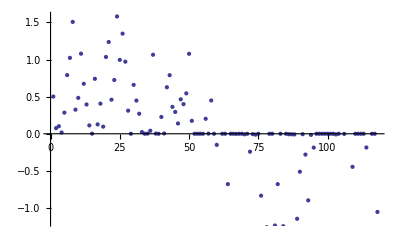

```mathematica
ListPlot[generalizedLinearModelFit["DevianceResiduals"]]
```

Cost function’s value at fitted parameters:

```mathematica
βFit=MapThread[Rule,{Evaluate[β],logit2["BestFitParameters"]}]
```

MapThread::mptd: Object logit2["BestFitParameters"] at position {2, 2} in MapThread[Rule, {{β0, β1, β2, β3, β4, β5, β6, β7, β8, β9, β10, β11, β12, β13, β14, β15, β16, β17, β18, β19, β20, β21, β22, β23, β24, β25, β26, β27}, logit2["BestFitParameters"]}] has only 0 of required 1 dimensions.

MapThread[Rule,{{β0,β1,β2,β3,β4,β5,β6,β7,β8,β9,β10,β11,β12,β13,β14,β15,β16,β17,β18,β19,β20,β21,β22,β23,β24,β25,β26,β27},logit2[BestFitParameters]}]

```mathematica
J[{β0,β1,β2},X1,y1]/.fittedParam
```

Power::infy: Infinite expression 1/0 encountered.

ReplaceAll::reps: {fittedParam} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ComplexInfinity/.fittedParam

### Decision boundary

```mathematica
Total[βFitNMinimize[[All,2]].nonLinearFeatures]==0
```

1.14213+0.601321 x1-1.87175 x1^2+0.126683 x1^3-1.42386 x1^4-0.243101 x1^5-1.03618 x1^6+1.16718 x2-0.915734 x1 x2-0.368731 x1^2 x2-0.0485564 x1^3 x2-0.207074 x1^4 x2+0.0292351 x1^5 x2-1.26953 x2^2-0.345184 x1 x2^2-0.60642 x1^2 x2^2-0.0431849 x1^3 x2^2-0.292622 x1^4 x2^2-0.173776 x2^3-0.269318 x1 x2^3-0.280281 x1^2 x2^3+0.0173668 x1^3 x2^3-1.16316 x2^4-0.286956 x1 x2^4-0.328972 x1^2 x2^4-0.469105 x2^5-0.13796 x1 x2^5-0.93199 x2^6==0

```mathematica
boundary=Composition[
Join@@#&,
With[{x1=#[[1]],y=#[[2]]},{x1,#}&/@y]&/@#&,
Cases[#,{_,{__}}]&,
{#,NSolve[Total[βFitNMinimize[[All,2]].ReplaceAll[nonLinearFeatures,x1-> #]]==0,x2]//Flatten//#[[All,2]]&//Cases[#,_Real]&}&/@#&
][Range[-1,1.5,0.001]];
```

{{-0.649,0.401108},{-0.649,0.416479},{-0.648,0.366953},{-0.648,0.448848},{-0.647,0.349637},{-0.647,0.464384},{-0.646,0.336094},{-0.646,0.476153},«2752»,{0.731,-0.0483969},{0.731,0.158162},{0.732,-0.0334873},{0.732,0.143493},{0.733,-0.0154102},{0.733,0.12566},{0.734,0.00941643},{0.734,0.101083}}

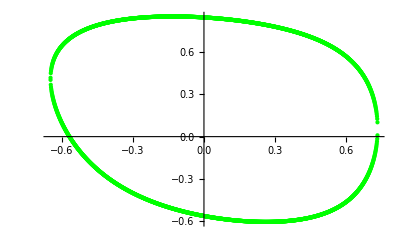

```mathematica
plotDecisionBoundary=ListPlot[boundary,PlotStyle-> Green]
```

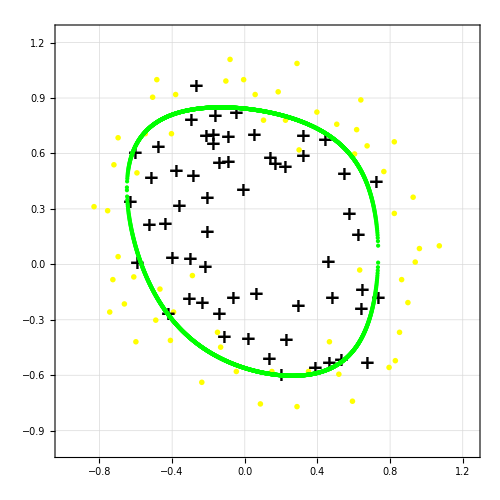

```mathematica
Show[{plotTrainingData,plotDecisionBoundary}]
```

### Prediction

```mathematica
Normal[logit2]
```

logit2

```mathematica
predictedProb[x1_,x2_]:=Block[
{β1,β2,sol},
sol=MapThread[Rule,{{β1,β2},{x1,x2}}];
Normal[logit2]/.sol
]
```

```mathematica
predictedProb[45,85]
```

logit2

### Prediction accuracy

```mathematica
predict[x1_,x2_]:=If[predictedProb[x1,x2]≥ 0.5,1,0]
```

```mathematica
Count[Map[predict@@#&,ex1]-y1,0]/Length[y1]//N
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0\ ComplexInfinity encountered.

Indeterminate

## Mathematica function reference

```mathematica
?LogitModelFit
```

LogitModelFit[{y_1,y_2,…},{f_1,f_2,…},x] constructs a binomial logistic regression model of the form 1/(1+ⅇ^(-(β_0+β_1 f_1 +β_2 f_2 +…))) that fits the y_i for successive x values 1, 2, ….
LogitModelFit[{{x_11,x_12,…,y_1},{x_21,x_22,…,y_2},…},{f_1,…},{x_1,x_2,…}] constructs a binomial logistic regression model of the form 1/(1+ⅇ^(-(β_0+β_1 f_1 +β_2 f_2 +…))) where the f_i depend on the variables x_k.
LogitModelFit[{m,v}] constructs a binomial logistic regression model from the design matrix m and response vector v.

```mathematica
?IncludeConstantBasis
```

IncludeConstantBasis is an option for LinearModelFit and other fitting functions that specifies whether a constant term should be included if not explicitly given in the list of basis functions.

IncludeConstantBasis is an option for LinearModelFit and other fitting functions that specifies whether a constant term should be included if not explicitly given in the list of basis functions.

```mathematica
?ArrayPlot
```

ArrayPlot[array] generates a plot in which the values in an array are shown in a discrete array of squares.

```mathematica
?NMinimize
```

NMinimize[f,x] minimizes f numerically with respect to x.
NMinimize[f,{x,y,…}] minimizes f numerically with respect to x, y, …. 
NMinimize[{f,cons},{x,y,…}] minimizes f numerically subject to the constraints cons.